```mathematica
Quit
```

```mathematica
n0=10^36; 
r0=10*10000;el=1;b0=10^14;c=1;
```

```mathematica
n[r_]=n0*(1-(r/r0)^2)
```

1000000000000000000000000000000000000 (1-r^2/10000000000)

```mathematica
Chi[x_,y_] = c/(4*Pi*n[Sqrt[x^2+y^2]]*el*y^2)
```

1/(4000000000000000000000000000000000000 π y^2 (1+(-x^2-y^2)/10000000000))

```mathematica
Chi0 =  c/(4*Pi*n0*el*r0^2);
```

```mathematica
BChi[x_,y_]=b0*r0*(Chi0/Chi[x,y])^2
```

1/10 y^4 (1+(-x^2-y^2)/10000000000)^2

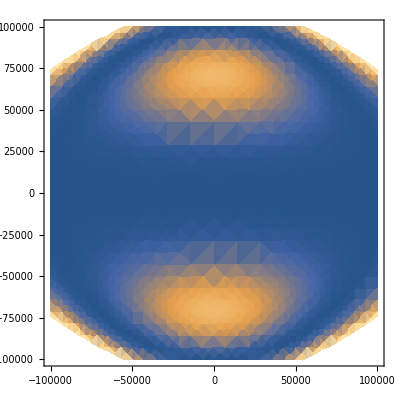

```mathematica
DensityPlot[BChi[x,y], {x,-r0,r0},{y,-r0,r0}]
```

```mathematica
BChiCyl[r_,theta_,z_]={0, BChi[z, r],b0}
```

{0,1/10 r^4 (1+(-r^2-z^2)/10000000000)^2,100000000000000}

```mathematica
dBdt=-Curl[Cross[c/(4*Pi*n[Sqrt[r^2+z^2]]*el)*Curl[BChiCyl[r,theta,z], {r,theta,z},"Cylindrical"],BChiCyl[r,theta,z]], {r,theta,z},"Cylindrical"]*HeavisideTheta[r0^2-r^2-z^2]
```

{-(r^4 HeavisideTheta[10000000000-r^2-z^2])/(1000000000000000000000000000000000 π),((r^7 z)/(2000000000000000000000000000000000000000000000000 π)-(r^9 z)/(10000000000000000000000000000000000000000000000000000000000 π)+(r^11 z)/(200000000000000000000000000000000000000000000000000000000000000000000 π)-(r^7 z^3)/(10000000000000000000000000000000000000000000000000000000000 π)+(r^9 z^3)/(100000000000000000000000000000000000000000000000000000000000000000000 π)+(r^7 z^5)/(200000000000000000000000000000000000000000000000000000000000000000000 π)) HeavisideTheta[10000000000-r^2-z^2],(r^3 z HeavisideTheta[10000000000-r^2-z^2])/(200000000000000000000000000000000 π)}

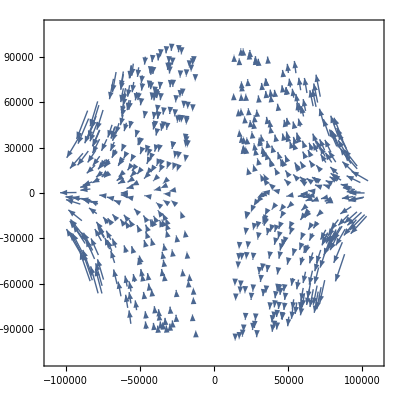

```mathematica
VectorPlot[{dBdt.{1,0,0},dBdt.{0,0,1}},{r,-r0,r0},{z,-r0,r0},VectorPoints->RandomReal[{-r0,r0},{1000,2}]]
```